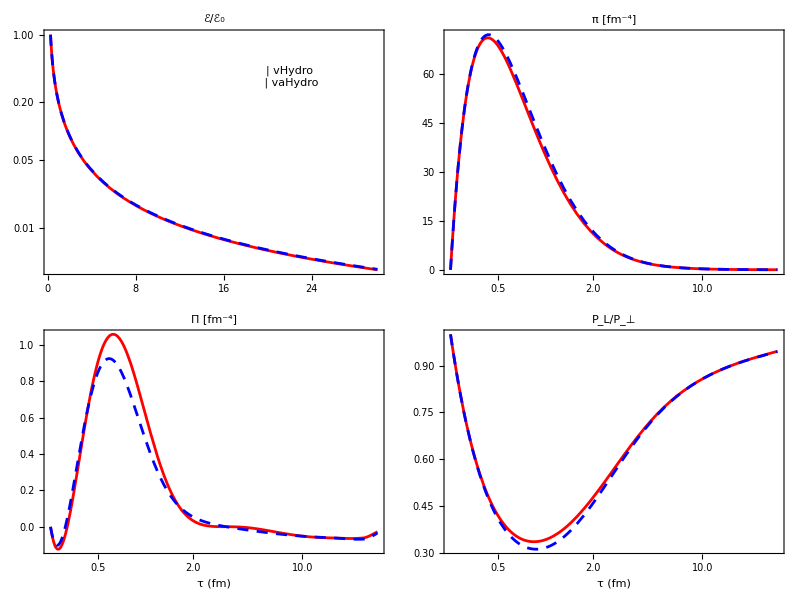

```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[];

stylesVH={Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],
Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]]};

stylesVAH={Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Directive[RGBColor[1,0,0],AbsoluteThickness[2]],
Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Directive[RGBColor[1,0,0],AbsoluteThickness[2]]};


(*//////////////////////////////////////////////////////////////*)


EnergyDensityDataRawVH=Import[wd<>"/eplot_vh.dat"];
piDataRawVH=Import[wd<>"/piplot_vh.dat"];
PiDataRawVH=Import[wd<>"/bulkplot_vh.dat"];
plptDataRawVH=Import[wd<>"/plptplot_vh.dat"];

EnergyDensityDataVH= Take[EnergyDensityDataRawVH,{2,Length[EnergyDensityDataRawVH]}];
piDataVH= Take[piDataRawVH,{2,Length[piDataRawVH]}];
PiDataVH= Take[PiDataRawVH,{2,Length[PiDataRawVH]}];
plptDataVH= Take[plptDataRawVH,{2,Length[plptDataRawVH]}];

energydensityVH = Interpolation[EnergyDensityDataVH[[All,{1,2}]]];
piVH = Interpolation[piDataVH[[All,{1,2}]]];
bulkVH = Interpolation[PiDataVH[[All,{1,2}]]];
plptVH = Interpolation[plptDataVH[[All,{1,2}]]];


(*//////////////////////////////////////////////////////////////*)
(*NAVIER STOKES*)

PiNSDataRawVH=Import[wd<>"/bulkNSplot.dat"];
PiNSDataVH= Take[PiNSDataRawVH,{2,Length[PiNSDataRawVH]}];
bulkNSVH = Interpolation[PiNSDataVH[[All,{1,2}]]];

piNSDataRawVH=Import[wd<>"/piNSplot.dat"];
piNSDataVH= Take[piNSDataRawVH,{2,Length[piNSDataRawVH]}];
piNSVH = Interpolation[piNSDataVH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)


EnergyDensityDataRawVAH=Import[wd<>"/eplot_vah.dat"];
piDataRawVAH=Import[wd<>"/piplot_vah.dat"];
PiDataRawVAH=Import[wd<>"/bulkplot_vah.dat"];
plptDataRawVAH=Import[wd<>"/plptplot_vah.dat"];

EnergyDensityDataVAH= Take[EnergyDensityDataRawVAH,{2,Length[EnergyDensityDataRawVAH]}];
piDataVAH= Take[piDataRawVAH,{2,Length[piDataRawVAH]}];
PiDataVAH= Take[PiDataRawVAH,{2,Length[PiDataRawVAH]}];
plptDataVAH= Take[plptDataRawVAH,{2,Length[plptDataRawVAH]}];

energydensityVH = Interpolation[EnergyDensityDataVH[[All,{1,2}]]];
piVH = Interpolation[piDataVH[[All,{1,2}]]];
bulkVH = Interpolation[PiDataVH[[All,{1,2}]]];
plptVH = Interpolation[plptDataVH[[All,{1,2}]]];

energydensityVAH = Interpolation[EnergyDensityDataVAH[[All,{1,2}]]];
piVAH = Interpolation[piDataVAH[[All,{1,2}]]];
bulkVAH = Interpolation[PiDataVAH[[All,{1,2}]]];
plptVAH = Interpolation[plptDataVAH[[All,{1,2}]]];


(*//////////////////////////////////////////////////////////////*)


t0 = EnergyDensityDataVAH[[1,1]];
tf = EnergyDensityDataVAH[[Length[EnergyDensityDataVAH],1]];

legend1=Panel[Grid[{{Graphics[{stylesVH[[1]],Line[{{0,0},{1,0}}]},ImageSize->28,AspectRatio->0.2],Style["vHydro",FontSize->16,FontFamily->"Calibri"]},
{Graphics[{stylesVAH[[1]],Line[{{0,0},{1,0}}]},ImageSize->28
,AspectRatio->0.2],Style["vaHydro",FontSize->16,FontFamily->"Calibri"]}}],Background->White];

energyplot=LogPlot[{energydensityVAH[t],energydensityVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVAH[[1]],stylesVH[[1]]},PlotLabel->Style["ℰ/ℰ_0",FontSize->18,FontFamily->"Calibri"],ImageSize->300,Frame->True,Axes->False,BaseStyle->{FontSize->14},AspectRatio->0.75,Epilog->Inset[legend1,{22,-1}]];
bulkplot =LogLinearPlot[{bulkVAH[t],bulkVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVAH[[1]],stylesVH[[1]]},ImageSize->300,PlotLabel->Style["Π [fm^-4]",FontSize->18,FontFamily->"Calibri"],FrameTicks->Automatic,Frame->True,Axes->False,FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],BaseStyle->{FontSize->14},AspectRatio->0.75];
piplot =LogLinearPlot[{piVAH[t],piVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVAH[[1]],stylesVH[[1]]},ImageSize->300,PlotLabel->Style["π [fm^-4]",FontSize->18,FontFamily->"Calibri"],Frame->True,Axes->False,BaseStyle->{FontSize->14},AspectRatio->0.75];
plptplot =LogLinearPlot[{plptVAH[t],plptVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVAH[[1]],stylesVH[[1]]},ImageSize->300,PlotLabel->Style["P_L/P_⊥",FontSize->18,FontFamily->"Calibri"],Frame->True,Axes->False,FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],BaseStyle->{FontSize->14},AspectRatio->0.75];

a1=Grid[{{energyplot,piplot},{bulkplot,plptplot}}]

Export["compare_hydro.pdf",a1];
```

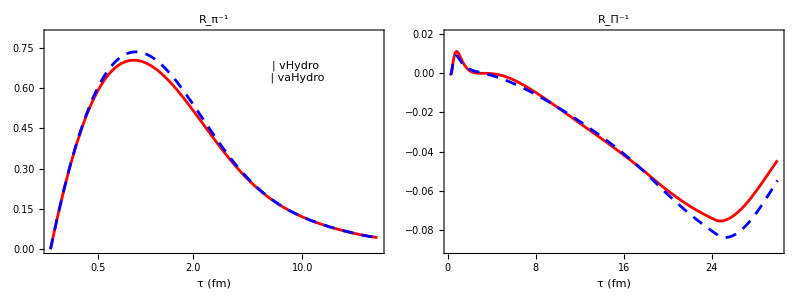

```mathematica
RpiInverseDataRawVH=Import[wd<>"/RpiInvplot_vh.dat"];
RbulkInverseDataRawVH=Import[wd<>"/RbulkInvplot_vh.dat"];

RpiInverseDataVH= Take[RpiInverseDataRawVH,{2,Length[RpiInverseDataRawVH]}];
RbulkInverseDataVH= Take[RbulkInverseDataRawVH,{2,Length[RbulkInverseDataRawVH]}];

RpiInverseVH = Interpolation[RpiInverseDataVH[[All,{1,2}]]];
RbulkInverseVH = Interpolation[RbulkInverseDataVH[[All,{1,2}]]];

RpiInverseDataRawVAH=Import[wd<>"/RpiInvplot_vah.dat"];
RbulkInverseDataRawVAH=Import[wd<>"/RbulkInvplot_vah.dat"];

RpiInverseDataVAH= Take[RpiInverseDataRawVAH,{2,Length[RpiInverseDataRawVAH]}];
RbulkInverseDataVAH= Take[RbulkInverseDataRawVAH,{2,Length[RbulkInverseDataRawVAH]}];

RpiInverseVAH = Interpolation[RpiInverseDataVAH[[All,{1,2}]]];
RbulkInverseVAH = Interpolation[RbulkInverseDataVAH[[All,{1,2}]]];

Rpi=LogLinearPlot[{RpiInverseVAH[t],RpiInverseVH[t]},{t,t0,tf},PlotRange->{0,0.8},PlotStyle->{stylesVAH[[1]],stylesVH[[1]]},ImageSize->{300},Frame->True,Axes->False,PlotLabel->Style["R_π^-1",FontSize->18,FontFamily->"Calibri"],FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],BaseStyle->{FontSize->14},AspectRatio->0.75,Epilog->Inset[legend1,{2.2,0.66}]];
Rbulk=Plot[{RbulkInverseVAH[t],RbulkInverseVH[t]},{t,t0,tf},PlotRange->{-0.09,0.02},PlotStyle->{stylesVAH[[1]],stylesVH[[1]]},ImageSize->300,Frame->True,Axes->False,PlotLabel->Style["R_Π^-1",FontSize->18,FontFamily->"Calibri"],FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],BaseStyle->{FontSize->14},AspectRatio->0.75];

Rplot=Grid[{{Rpi,Rbulk}}]

Export["compare_R.pdf",Rplot];
```

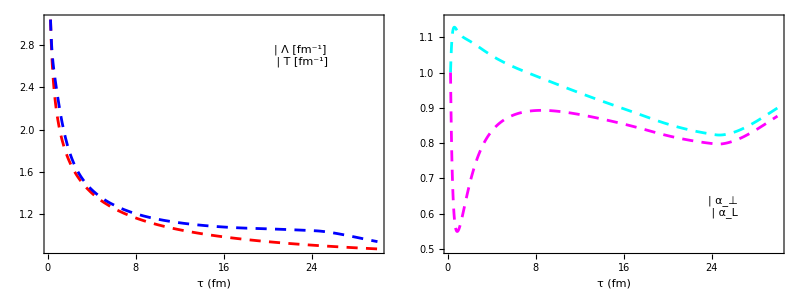

```mathematica
TDataRaw=Import[wd<>"/Tplot_vah.dat"];
lambdaDataRaw=Import[wd<>"/lambdaplot_vah.dat"];
axDataRaw=Import[wd<>"/axplot_vah.dat"];
azDataRaw=Import[wd<>"/azplot_vah.dat"];

TData= Take[TDataRaw,{2,Length[TDataRaw]}];
lambdaData= Take[lambdaDataRaw,{2,Length[lambdaDataRaw]}];
axData= Take[axDataRaw,{2,Length[axDataRaw]}];
azData= Take[azDataRaw,{2,Length[azDataRaw]}];


T = Interpolation[TData[[All,{1,2}]]];
lambda = Interpolation[lambdaData[[All,{1,2}]]];
ax = Interpolation[axData[[All,{1,2}]]];
az = Interpolation[azData[[All,{1,2}]]];

legendtemp=Panel[Grid[{{Graphics[{Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Line[{{0,0},{1,0}}]},ImageSize->28,AspectRatio->0.2],Style["Λ [fm^-1]",FontSize->16,FontFamily->"Calibri"]},
{Graphics[{Directive[RGBColor[1,0,0],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Line[{{0,0},{1,0}}]},ImageSize->28,AspectRatio->0.2],Style["T [fm^-1]",FontSize->16,FontFamily->"Calibri"]}}],Background->White];

legendalpha=Panel[Grid[{{Graphics[{Directive[RGBColor[0,1,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Line[{{0,0},{1,0}}]},ImageSize->28,AspectRatio->0.2],Style["α_⊥",FontSize->16,FontFamily->"Calibri"]},
{Graphics[{Directive[RGBColor[1,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Line[{{0,0},{1,0}}]},ImageSize->28,AspectRatio->0.2],Style["α_L",FontSize->16,FontFamily->"Calibri"]}}],Background->White];

temp=Plot[{T[t],lambda[t]},{t,t0,tf},PlotRange->All,PlotStyle->{Directive[RGBColor[1,0,0],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]]},ImageSize->300,Frame->True,Axes->False,FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],BaseStyle->{FontSize->14},AspectRatio->0.75,Epilog->Inset[legendtemp,{23,2.7}]];
alpha=Plot[{ax[t],az[t]},{t,t0,tf},PlotRange->{0.5,1.15},PlotStyle->{Directive[RGBColor[0,1,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[RGBColor[1,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]]},ImageSize->300,Frame->True,Axes->False,FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],BaseStyle->{FontSize->14},AspectRatio->0.75,Epilog->Inset[legendalpha,{25,0.62}]];

anisoplot=Grid[{{temp,alpha}}]

Export["aniso1.pdf",anisoplot];
```

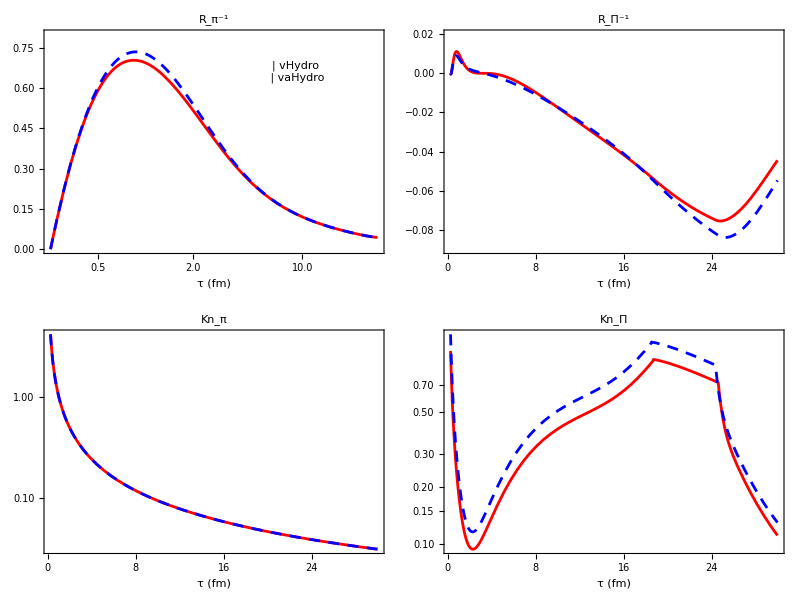

```mathematica
taupiDataRawVH=Import[wd<>"/taupiplot_vh.dat"];
taubulkDataRawVH=Import[wd<>"/taubulkplot_vh.dat"];

taupiDataVH= Take[taupiDataRawVH,{2,Length[taupiDataRawVH]}];
taubulkDataVH= Take[taubulkDataRawVH,{2,Length[taubulkDataRawVH]}];

taupiVH = Interpolation[taupiDataVH[[All,{1,2}]]];
taubulkVH = Interpolation[taubulkDataVH[[All,{1,2}]]];

taupiDataRawVAH=Import[wd<>"/taupiplot_vah.dat"];
taubulkDataRawVAH=Import[wd<>"/taubulkplot_vah.dat"];

taupiDataVAH= Take[taupiDataRawVAH,{2,Length[taupiDataRawVAH]}];
taubulkDataVAH= Take[taubulkDataRawVAH,{2,Length[taubulkDataRawVAH]}];

taupiVAH = Interpolation[taupiDataVAH[[All,{1,2}]]];
taubulkVAH = Interpolation[taubulkDataVAH[[All,{1,2}]]];

Knpi=LogPlot[{Sqrt[1.5]*taupiVH[t]/t,Sqrt[1.5]*taupiVAH[t]/t},{t,t0,tf},PlotRange->Automatic,PlotStyle->{stylesVAH[[1]],stylesVH[[1]]},ImageSize->300,Frame->True,Axes->False,PlotLabel->Style["Kn_π",FontSize->18,FontFamily->"Calibri"],FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],BaseStyle->{FontSize->14},AspectRatio->0.75(*,Epilog->Inset[legend1,{2.2,0.66}]*)];
Knbulk=LogPlot[{taubulkVH[t]/t,Sqrt[1.5]*taubulkVAH[t]/t},{t,t0,tf},PlotStyle->{stylesVAH[[1]],stylesVH[[1]]},ImageSize->300,Frame->True,Axes->False,PlotLabel->Style["Kn_Π",FontSize->18,FontFamily->"Calibri"],FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],BaseStyle->{FontSize->14},AspectRatio->0.75];

Rplot=Grid[{{Knpi,Knbulk}}];

Export["compare_Kn.pdf",Rplot];

a2=Grid[{{Rpi,Rbulk},{Knpi,Knbulk}}]

Export["compare_validity.pdf",a2];
```